# Numerical Methods for Solving ODEs

#### Name: Samriddha Ganguly Roll Number: 22279

## The Runge-Kutta 4th Order Method:

```mathematica
rk4[func_,X0_,tf_,nmax_]:=Module[{h,datalist,prev,next,rate1,rate2,rate3,rate4},h=(tf-X0⟦1⟧)/nmax//N;
For[datalist={X0},Length[datalist]≤nmax,AppendTo[datalist,next],prev=Last[datalist];
rate1=Through[func@@prev];
rate2=Through[func@@(prev+h/2rate1)];
rate3=Through[func@@(prev+h/2rate2)];
rate4=Through[func@@(prev+h rate3)];
next=prev+h/6(rate1+2rate2+2rate3+rate4);];
Return[datalist];]
```

```mathematica
w=79;
β=Sqrt[w-0.25];
2.0Pi/β;
id[t_,charge_,current_]=1;
chargedot[t_,charge_,current_]=current;
currentdot[t_,charge_,current_]=-w charge-current;
initial={0,1,0};
solndata=rk4[{id,chargedot,currentdot},initial,10,100];
```

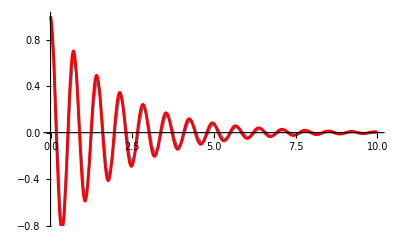

```mathematica
Show[ListPlot[solndata⟦;;,1;;2⟧,Joined->True,PlotRange->Full],Plot[Exp[-t/2 ] Cos[β t],{t,0,10},PlotStyle->Red, PlotRange->Full]]
```

## The Runge-Kutta 2nd Order Method :

```mathematica
Clear["Global`*"]
```

```mathematica
rk2[func_,X0_,tf_,nmax_]:=Module[{h,datalist,prev,next,next1,rate,rate1},h=(tf-X0⟦1⟧)/nmax//N;
For[datalist={X0},Length[datalist]≤nmax,AppendTo[datalist,next],prev=Last[datalist];
rate=Through[func@@prev];
next1=prev+h rate;
rate1=Through[func@@next1];
next=prev+h/2(rate+rate1);];
Return[datalist];]
```

```mathematica
w=79;
β=Sqrt[w-0.25];
2.0Pi/β;
id[t_,charge_,current_]=1;
chargedot[t_,charge_,current_]=current;
currentdot[t_,charge_,current_]=-w charge-current;
initial={0,1,0};
solndata=rk2[{id,chargedot,currentdot},initial,10,600];
```

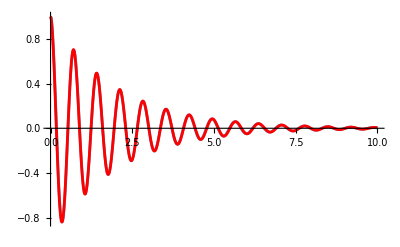

```mathematica
Show[ListPlot[solndata⟦;;,1;;2⟧,Joined->True,PlotRange->Full],Plot[Exp[-t/2 ] Cos[β t],{t,0,10},PlotStyle->Red, PlotRange->Full]]
```

## The Euler Method:

```mathematica
Clear["Global`*"]
```

```mathematica
euler[func_,X0_,tf_,nmax_]:=Module[{h,datalist,prev,next,rate},h=(tf-X0⟦1⟧)/nmax//N;
For[datalist={X0},Length[datalist]≤nmax,AppendTo[datalist,next],prev=Last[datalist];
rate=Through[func@@prev];
next=prev+h rate;];
Return[datalist];]
```

```mathematica
w=79;
β=Sqrt[w-0.25];
2.0Pi/β;
id[t_,charge_,current_]=1;
chargedot[t_,charge_,current_]=current;
currentdot[t_,charge_,current_]=-w charge-current;
initial={0,1,0};
solndata=euler[{id,chargedot,currentdot},initial,10,10000];
```

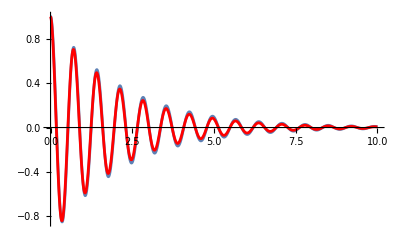

```mathematica
Show[ListPlot[solndata⟦;;,1;;2⟧,Joined->True,PlotRange->Full],Plot[Exp[-t/2 ] Cos[β t],{t,0,10},PlotStyle->Red, PlotRange->Full]]
```

## The Error Function to exhibit error with respect to step size h:

```mathematica
err[dataset_,func_]:=Module[{tlist,xlist,fxlist},tlist=dataset⟦;;,1⟧;
xlist=dataset⟦;;,2⟧;
fxlist=func/@tlist;
Return[xlist-fxlist//Abs//Mean];]
```

```mathematica
solfunc[t_]=Exp[-t/2 ] Cos[β t]
```

ⅇ^(-t/2) Cos[8.87412 t]

```mathematica
err[solndata,solfunc]
```

0.00557572